# Acoustic Gravity Waves

Following Vallis (2017), Ch 7.8.

```mathematica
omega = Solve[ω^4 - cs2 ω^2 ( k^2 + m^2 + 1/(4H2)) + cs2 N2 k^2 == 0, ω]
```

{{ω→-(√(cs2/H2+4 cs2 k^2+4 cs2 m^2-√((-cs2/H2-4 cs2 k^2-4 cs2 m^2)^2-64 cs2 k^2 N2)))/(2 √2)},{ω→(√(cs2/H2+4 cs2 k^2+4 cs2 m^2-√((-cs2/H2-4 cs2 k^2-4 cs2 m^2)^2-64 cs2 k^2 N2)))/(2 √2)},{ω→-(√(cs2/H2+4 cs2 k^2+4 cs2 m^2+√((-cs2/H2-4 cs2 k^2-4 cs2 m^2)^2-64 cs2 k^2 N2)))/(2 √2)},{ω→(√(cs2/H2+4 cs2 k^2+4 cs2 m^2+√((-cs2/H2-4 cs2 k^2-4 cs2 m^2)^2-64 cs2 k^2 N2)))/(2 √2)}}

```mathematica
omega/.H2->1/.N2->1/.cs2->0.8/4/.m->0
```

{{ω→-(√(0.2+0.8 k^2-√(-12.8 k^2+(-0.2-0.8 k^2)^2)))/(2 √2)},{ω→(√(0.2+0.8 k^2-√(-12.8 k^2+(-0.2-0.8 k^2)^2)))/(2 √2)},{ω→-(√(0.2+0.8 k^2+√(-12.8 k^2+(-0.2-0.8 k^2)^2)))/(2 √2)},{ω→(√(0.2+0.8 k^2+√(-12.8 k^2+(-0.2-0.8 k^2)^2)))/(2 √2)}}

The standard plot for these is letting m be a parameter (here m=0 is blue and m=1 is gold) and showing the modes varying with k. 

Note that the Lamb wave is not on here.

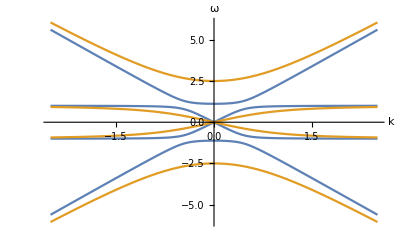

```mathematica
p1 = Plot[{ω/.omega/.H2->1/.N2->1/.cs2->4/0.8/.m->0, ω/.omega/.H2->1/.N2->1/.cs2->4/0.8/.m->1},{k,-2.5,2.5}, AxesLabel->{k, ω}]
```

Now, what happens if we let k be zero and vary m? As you might expect, with k = 0, the gravity modes are zero frequency and doubly degenerate. Interestingly, even for that case (blue lines), the acoustic waves have a cutoff: there are no acoustic modes with frequencies less than 1ish. This is very different than when you have just 1-D acoustic modes without stratification.

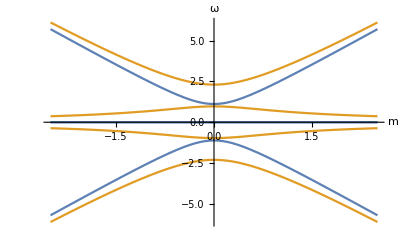

```mathematica
p2= Plot[{ω/.omega/.H2->1/.N2->1/.cs2->4/0.8/.k->0, ω/.omega/.H2->1/.N2->1/.cs2->4/0.8/.k->1},{m,-2.5,2.5}, AxesLabel->{m, ω}]
```